```mathematica
Quit
```

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files (x86)\Microsoft Visual Studio 14.0,CompilerName→Automatic}}

```mathematica
If[ValueQ[lib]&&StringQ[lib]&&FileExistsQ[lib],DeleteFile[lib]];
lib=CreateLibrary[
{"C:\\Users\\Wolfram\\Desktop\\nik\\repos\\wolfram-2017\\project\\CSource\\libtinslink.cpp"},
"libtinslink",
"IncludeDirectories"->{"C:\\Users\\Wolfram\\Downloads\\libtins-debug\\libtins\\include","C:\\Users\\Wolfram\\Downloads\\winpcap\\WpdPack\\Include"},
"LibraryDirectories"->{"C:\\Users\\Wolfram\\Downloads\\libtins-debug\\libtins\\lib","C:\\Users\\Wolfram\\Downloads\\winpcap\\WpdPack\\Lib\\x64"},
"Libraries"->{"tins","wpcap","Iphlpapi","Ws2_32"},
"Language"->"C++",
"Defines"->{"WIN32","TINS_STATIC","_DEBUG"},
"CompileOptions"->{"/MDd"},
"TargetDirectory"->"C:\\Users\\Wolfram\\Desktop"
]
```

C:\Users\Wolfram\Desktop\libtinslink.dll

```mathematica
LibraryLoad[lib]
```

```mathematica
listDefaultInterface=LibraryFunctionLoad[lib,"listDefaultInterface",{},{String}]
listAllInterfaces=LibraryFunctionLoad[lib,"listAllInterfaces",{},{Integer,1}]

startDNSSniff=LibraryFunctionLoad[lib,"startDNSSniff",{String},"Void"]
stopDNSSniff=LibraryFunctionLoad[lib,"stopDNSSniff",{},"Void"]
EmptyDNSSniffingHashTable=LibraryFunctionLoad[lib,"EmptyDNSSniffingHashTable",{},{Integer,1}]

StartTCPSniffing=LibraryFunctionLoad[lib,"StartTCPSniffing",{String},"Void"]
StopTCPSniffing=LibraryFunctionLoad[lib,"StopTCPSniffing",{},"Void"]
EmptyTCPSniffingHashTable=LibraryFunctionLoad[lib,"EmptyTCPSniffingHashTable",{},{Integer,1}]

StartUDPSniffing=LibraryFunctionLoad[lib,"StartUDPSniffing",{String},"Void"]
StopUDPSniffing=LibraryFunctionLoad[lib,"StopUDPSniffing",{},"Void"]
EmptyUDPSniffingHashTable=LibraryFunctionLoad[lib,"EmptyUDPSniffingHashTable",{},{Integer,1}]
```

LibraryFunction[…]

LibraryFunction[…]

LibraryFunction[…]

«8 more identical outputs»

```mathematica
LISTING INTERFACES
```

```mathematica
listAllInterfaces[]
```

```mathematica
printInterfaces[list__] := FromCharacterCode/@DeleteCases[SplitBy[list,#===0&],{0}]
```

```mathematica
printInterfaces[listAllInterfaces[]]
```

{{1AA5A598-CD4F-4EDE-AE5A-050F617880C2},{763694AC-5744-47D8-94B3-561E2894AF7E},{846EE342-7039-11DE-9D20-806E6F6E6963},{97232E8A-7703-4DD7-8F9A-59EF7C9C7EF3}}

```mathematica
listDefaultInterface[]
```

{1AA5A598-CD4F-4EDE-AE5A-050F617880C2}

```mathematica
SNIFFING DNS Domains
```

```mathematica
DNSSniff[x__]:=Module[{x0 = x},
startDNSSniff[listDefaultInterface[]];
Pause[x0];
stopDNSSniff[];
k = FromCharacterCode/@DeleteCases[SplitBy[EmptyDNSSniffingHashTable[],#===0&],{0}];
k
]
```

```mathematica
DNSSniff[5]
```

{www.google.com,ogs.google.com,www.google.com,ogs.google.com,awer.com,awer.com,domainmanager.blob.core.windows.net,fonts.googleapis.com,fonts.gstatic.com,clients4.google.com,fonts.googleapis.com,domainmanager.blob.core.windows.net,fonts.gstatic.com,clients4.google.com}

```mathematica
CAPTURING TCP DATA
```

```mathematica
(StartTCPSniffing[listDefaultInterface[]];
Pause[10];
StopTCPSniffing[];
data=EmptyTCPSniffingHashTable[];
rest=data;
Dataset@First@Last@Reap[While[rest=!={},
(
{{len},rest}=TakeDrop[rest,1];
{packet,rest}=TakeDrop[rest,len];
{{strLen},payload}=TakeDrop[packet,1];
{str,payload}=TakeDrop[payload,strLen];
k=FromCharacterCode[str];
y1=AssociationThread[{"SourceIP","SourcePort","DestinationIP","DestinationPort","SequenceNumber","AcknowledgementSequenceNumber","Window","Checksum","Urgent Pointer","Data Offset","Flags","Header Size","TimeSeconds","TimeMicroseconds"},StringTrim/@StringSplit[k,{":","to","seq","ack_seq","window","checksum","urgentpointer","dataoffset","flags","headersize","ts","tus"}]];
y1=Append[KeyDrop[{"TimeSeconds","TimeMicroseconds"}]@y1,"Timestamp"->FromUnixTime@FromDigits@y1["TimeSeconds"]+Quantity[FromDigits[y1["TimeMicroseconds"]],"Microseconds"]];
Sow[Append[MapAt[ToCharacterCode[#,"UTF8"]&,Key["Data Offset"]]@y1,"Payload"->ByteArray[payload]]]
)
]
])
```

Dataset[<>]

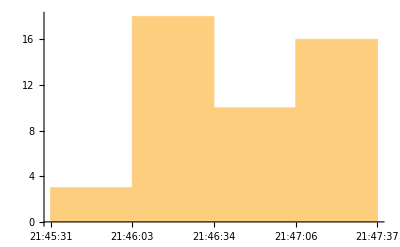

```mathematica
DateHistogram[Normal[First[GroupBy[%21,"SourceIP"]][All,"Timestamp"]]]
```

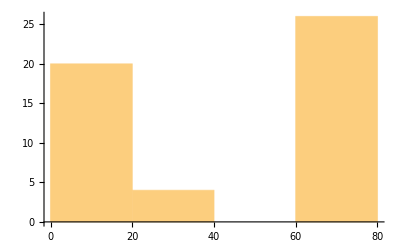

```mathematica
Histogram[Length/@Normal[First[GroupBy[%21,"SourceIP"]][All,"Payload"]]]
```

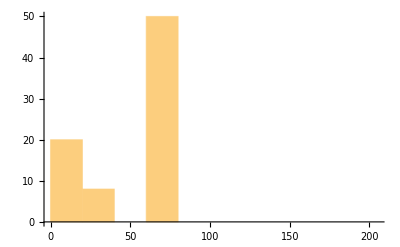

```mathematica
Histogram[Length/@Normal[%21[All,"Payload"]]]
```

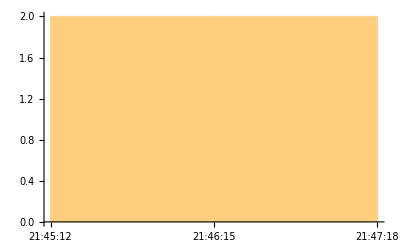

```mathematica
DateHistogram[Last[GroupBy[%21,"SourceIP"]][All,"Timestamp"]]
```

```mathematica
FromCharacterCode@*Normal/@Normal@Select[%21,#["SourcePort"]=="49271"&][All,"Payload"]
```

```mathematica
CAPTURING UDP DATA
```

```mathematica
(StartUDPSniffing[listDefaultInterface[]];
Pause[5];
StopUDPSniffing[];
data=EmptyUDPSniffingHashTable[];
rest=data;
Dataset@First@Last@Reap[Quiet[While[rest=!={},
(
{{len},rest}=TakeDrop[rest,1];
{packet,rest}=TakeDrop[rest,len];
{{strLen},payload}=TakeDrop[packet,1];
{str,payload}=TakeDrop[payload,strLen];
k=FromCharacterCode[str];
y1=AssociationThread[{"SourceIP","SourcePort","DestinationIP","DestinationPort","Checksum","Length","Header Size", "TimeSeconds", "TimeMicroseconds"},StringTrim/@StringSplit[k,{":","to","checksum","length","headersize", "ts", "tus"}]];
y1=Append[KeyDrop[{"TimeSeconds","TimeMicroseconds"}]@y1,"Timestamp"->FromUnixTime@FromDigits@y1["TimeSeconds"]+Quantity[FromDigits[y1["TimeMicroseconds"]],"Microseconds"]];
Sow[Append[y1,"Payload"->ByteArray[payload]]]
)
]]
])
```

Dataset[<>]